```mathematica
Clear["Global`*"]
XY1={{-1,3},{0,0.5},{0.5,0},{1,1}};
f1[x_]:=InterpolatingPolynomial[XY1,x];
Print[{f1[0.25],f1[0.75]}];

XY2={{-1,1.5},{0,0},{0.5,0},{1,0.5}};
f2[x_]:=InterpolatingPolynomial[XY2,x];
Print[{f2[-0.25],f2[0.25]}];
```

{0.109375,0.265625}

{0.1875,-0.0625}

2.07897+2.09235 x

1.94449+2.0851 x+0.28191 x^2

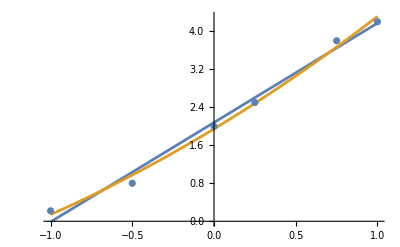

```mathematica
Clear["Global`*"]
XY={{-1,0.22},{-0.5,0.8},{0,2},{0.25,2.5},{0.75,3.8},{1,4.2}};
Linear=Fit[XY,{1,x},x]
Quad=Fit[XY,{1,x,x^2},x]
Show[Plot[{Linear,Quad},{x,-1,1}],ListPlot[XY]]
```

-2.37227+0.0573264 x^2

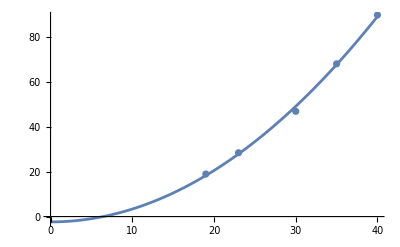

```mathematica
Clear["Global`*"]
XY={{19,19.0},{23,28.5},{30,47.0},{35,68.2},{40,90.0}};
SQuad=Fit[XY,{1,x^2},x]
Show[Plot[{SQuad},{x,0,40}],ListPlot[XY]]
```

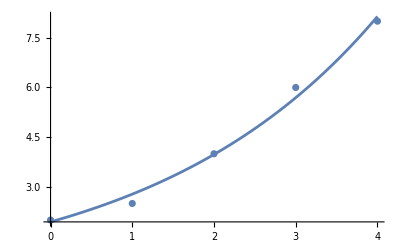

```mathematica
Clear["Global`*"]
XY={{0,2},{1,2.5},{2,4},{3,6},{4,8}};
Model=a*Exp[b*x];
Solution=FindFit[XY,Model,{a,b},x];
SExp[x_]:=Model/.Solution;
Show[Plot[{SExp[x]},{x,0,4}],ListPlot[XY]]
```

```mathematica
Clear["Global`*"]
FindMinimum[Sin[x]Cos[x],{x,0.5}]
FindMinimum[Sin[x*y*Exp[x^2]],{x,0.2},{y,0.3}]
```

{-0.5,{x→-0.785398}}

{-1.,{x→-1.35561,y→0.184453}}

```mathematica
Clear["Global`*"]
c1={-3,-2};
A1={{1,-2},{-3,-2},{-1,1},{1,0},{0,1}};
b1={-4,-14,-3,0,0};
{x1=LinearProgramming[c1,A1,b1],-c1.x1}

c2={2,3,4};
A2={{1,2,-1},{1,1,-1},{0,1,2},{1,0,0},{0,1,0},{0,0,1}};
b2={10,60,12,0,0,1.000001};
{x2=LinearProgramming[c2,A2,b2],c2.x2}
```

{{4,1},14}

{{51.,10.,1.},136.}

{{y[x]→1/4 (-2 Cos[x]+2 Cos[x]^3+2 x Sin[x]+Sin[x] Sin[2 x])}}

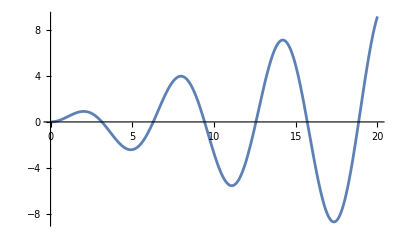

{{u[t]→InterpolatingFunction[…][t],v[t]→InterpolatingFunction[…][t]}}

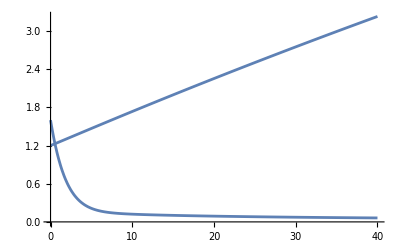

{{u[t,x]→InterpolatingFunction[…][t,x]}}

-Graphics3D-

{{u[t,x]→InterpolatingFunction[{{0., 40.}, {…, -10., 10., …}}, <>][t,x]}}

-Graphics3D-

```mathematica
Clear["Global`*"]
Q1=DSolve[{y''[x]+y[x]==Cos[x],
y'[0]==0,
y[0]==0},y[x],x]
Plot[y[x]/.Q1[[1]],{x,0,20}]

Q2=NDSolve[{u'[t]==0.09*(1-u[t]/20)-0.45*u[t]*v[t],v'[t]==0.06*(1-v[t]/15)-0.001*u[t]*v[t],
u[0]==1.6,
v[0]==1.2},{u[t],v[t]},{t,0,40}]
Plot[{u[t],v[t]}/.Q2[[1]],{t,0,40}]

Q3=NDSolve[{D[u[t,x],t]==D[D[u[t,x],x],x],
u[0,x]==0,
u[t,0]==Sin[t],
u[t,5]==0},u[t,x],{t,0,10},{x,0,5}]
Plot3D[u[t,x]/.Q3[[1]],{t,0,10},{x,0,5}]

Q4=NDSolve[{D[u[t,x],{t,2}]==D[u[t,x],{x,2}],
u[0,x]==Exp[-x^2],
u[t,-10]==u[t,10],
D[u[t,x],t]==0/.t->0},u[t,x],{t,0,40},{x,-10,10}]
Plot3D[u[t,x]/.Q4[[1]],{t,0,40},{x,-10,10}]
```